2026-07-27--jam99--ThetaI-rewrite-v4.nb

John A . Marohn (jam99@cornell.edu)
2026-07-28

Confirm that Lekkala2013 Equation 17, rewritten, agrees with the equation I have coded in Python.

## From 2023-09-23--jam99--ThetaI-rewrite-v2.nb

We wish to rewrite  Equation 17 in Lekkala2013, J. Chem. Phys. (2013) 139:184702.  
Write out the numerator and denominator in Lekkala2013 θ_I separately, with θ1 = k h_s and θ2 = η h_s.
Lekkala writes

	θ_I(k,ω) = (ϵ_s(ω))/(ϵ_eff(ω))[- λ Coth[θ1] + numerator/denominator]
	
Below we rewrite the part in braces.  In my code, I compute

	(θ_I(k,ω))/(ϵ_s(ω)) = 1/(ϵ_eff(ω))[- λ Coth[θ1] + numerator/denominator]	
	
which we recognize as the part in braces divided by ϵ_eff(ω).

```mathematica
numerator = Sinh[θ1] Sinh[θ2] + α Cosh[θ1]Sinh[θ2]- λ Cosh[θ1] Cosh[θ2] + 2 λ - λ^2 Sinh[θ1]/Sinh[θ2]
```

2 λ-λ Cosh[θ1] Cosh[θ2]-λ^2 Csch[θ2] Sinh[θ1]+α Cosh[θ1] Sinh[θ2]+Sinh[θ1] Sinh[θ2]

```mathematica
denominator = Cosh[θ1] Sinh[θ2] +α Sinh[θ1]Sinh[θ2]- λ Sinh[θ1] Cosh[θ2]
```

-λ Cosh[θ2] Sinh[θ1]+Cosh[θ1] Sinh[θ2]+α Sinh[θ1] Sinh[θ2]

Divide the denominator by Cosh[θ] to see if that tames the θ1 divergence.

```mathematica
denominator/Cosh[θ1] // Simplify
```

Sinh[θ2]-λ Cosh[θ2] Tanh[θ1]+α Sinh[θ2] Tanh[θ1]

It does ...

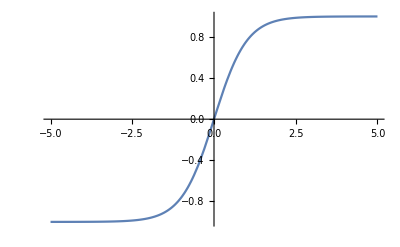

```mathematica
Plot[{Tanh[θ1]},{θ1,-5,5}]
```

... but the θ2 functions in the denominator still diverge.

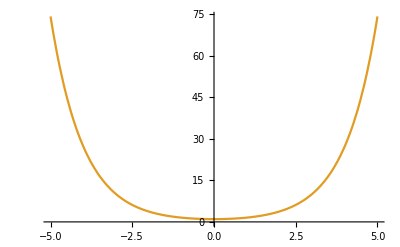

```mathematica
Plot[{Sinh[θ],Cosh[θ2]},{θ2,-5,5}]
```

Try dividing the denominator by Cosh[θ1]Cosh[θ2].

```mathematica
denominator/(Cosh[θ1]Cosh[θ2]) // Simplify
```

Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])

```mathematica
Plot[Tanh[θ2],{θ2,-5,5}]
```

-Graphics-

Now, by inspection, both the θ1 and θ2 functions in the denominator are well-behaved.  What about the numerator?

```mathematica
numerator/(Cosh[θ1]Cosh[θ2]) // Simplify
```

-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2]

All three θ2 functions in the numerator are ok at large θ2.  But one of them diverges at small θ2, which is a problem.

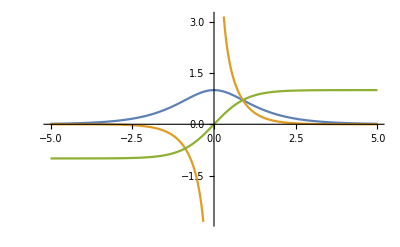

```mathematica
Plot[{Sech[θ2],Csch[θ2] Sech[θ2],Tanh[θ2]},{θ2,-5,5}]
```

This function is the culprit.

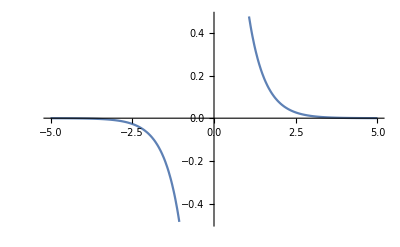

```mathematica
Plot[Csch[θ2] Sech[θ2],{θ2,-5,5}]
```

The argument θ2 = η h_s in the paper, and η does not go to zero.  So, in practice, I think the function Csch[θ2] Sech[θ2] should be ok.

In summary, write the big fraction θ_I as follows

```mathematica
(-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2])/(Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])) ;
```

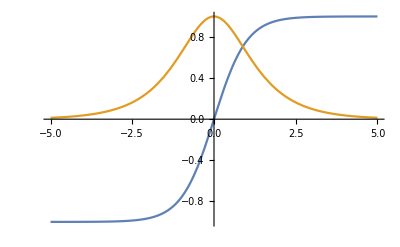

```mathematica
Plot[{Tanh[θ2],Sech[θ2]},{θ2,-5,5}]
```

Python does not have Sech and Csch function.  However, note that

```mathematica
1/Sech[θ1]
```

Cosh[θ1]

```mathematica
1/Csch[θ2]
```

Sinh[θ2]

So let us implement θ_I as (we are leaving out the ϵ_s/ϵ_eff prefactor here)

```mathematica
θI=-λ Coth[θ2]+(Tanh[θ1] Tanh[θ2]+ α Tanh[θ2]-λ+2 λ /(Cosh[θ1] Cosh[θ2])-λ^2 Tanh[θ1] /(Cosh[θ2] Sinh[θ2]) )/(Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2])) ;
```

Expand the denominator

```mathematica
Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2]) // Expand
```

-λ Tanh[θ1]+Tanh[θ2]+α Tanh[θ1] Tanh[θ2]

Check that this expression agrees with what we started with.

```mathematica
θI -( -λ Coth[θ2]+numerator/denominator) // FullSimplify
```

0

This form is well behaved because θ2 does not go to zero.  Check the large h_s limit, where θ1 and θ2 go to infinity.

```mathematica
Limit[θI,{θ1-> Infinity,θ2-> Infinity}]
```

1-λ

## Check the Mathematica result against my code

### Forward substitution

Rewrite the Mathematica expression in terms of my variables p1 through p7.

```mathematica
θI
```

-λ Coth[θ2]+(-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2])/(Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2]))

Divide the numerator in the second term by ϵ_eff^2and use the variables defined in my code to rewrite the answer:

```mathematica
((-λ+2 λ Sech[θ1] Sech[θ2]-λ^2 Csch[θ2] Sech[θ2] Tanh[θ1]+α Tanh[θ2]+Tanh[θ1] Tanh[θ2])/ϵ$eff^2 // Expand ) /. { 1/ϵ$eff^2-> p2,α/ϵ$eff^2-> p3,λ/ϵ$eff^2-> - p4, λ^2/ϵ$eff^2-> -p5}
```

p4-2 p4 Sech[θ1] Sech[θ2]+p5 Csch[θ2] Sech[θ2] Tanh[θ1]+p3 Tanh[θ2]+p2 Tanh[θ1] Tanh[θ2]

This looks like the numerator in my code.

Divide the denominator in the second term by ϵ_effand use the variables in my code to rewrite the answer:

```mathematica
((Tanh[θ2]+Tanh[θ1] (-λ+α Tanh[θ2]))/ϵ$eff // Expand ) /. {-λ/ϵ$eff-> p1, α/ϵ$eff-> p7,  1/ϵ$eff-> p6} // Simplify
```

p6 Tanh[θ2]+Tanh[θ1] (p1+p7 Tanh[θ2])

This looks like the denominator in my code.

### Backward substitution

Now write out my equation with θ1 and θ2 swapped.  My coded equation θI$code is really θ_I/ϵ_s, as note above.
Substitute for the variables p1 through p7.

```mathematica
θI$code = p1 Coth[θ2] + (p2 Tanh[θ1] Tanh[θ2] + p3 Tanh[θ2] + p4 - 2 p4 Sech[θ1]Sech[θ2] + p5 Tanh[θ1] Sech[θ2] Csch[θ2])/(p6 Tanh[θ2] + Tanh[θ1](p1 + p7 Tanh[θ2])) ;
```

```mathematica
θI$code$sub =  θI$code /. {p1 -> -λ/ϵ$eff,p2-> 1/ϵ$eff^2,p3->α/ϵ$eff^2,p4-> -λ/ϵ$eff^2,p5->-λ^2/ϵ$eff^2 ,p6-> 1/ϵ$eff,p7-> α/ϵ$eff}
```

-(λ Coth[θ2])/ϵ$eff+(-λ/ϵ$eff^2+(2 λ Sech[θ1] Sech[θ2])/ϵ$eff^2-(λ^2 Csch[θ2] Sech[θ2] Tanh[θ1])/ϵ$eff^2+(α Tanh[θ2])/ϵ$eff^2+(Tanh[θ1] Tanh[θ2])/ϵ$eff^2)/(Tanh[θ2]/ϵ$eff+Tanh[θ1] (-λ/ϵ$eff+(α Tanh[θ2])/ϵ$eff))

Check that the resulting expression agrees with the Mathematica result.  As noted above, we should divide θI, “the part in braces”, by ϵ_eff to obtain θ_I/ϵ_s.

```mathematica
θI/ϵ$eff - θI$code$sub// Simplify
```

0